Distribution.txt

ErrorList.txt

-Graphics3D-

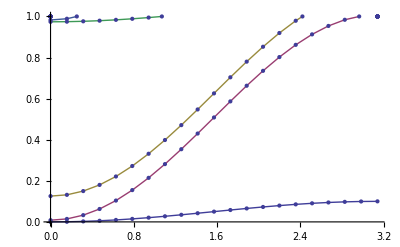

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
Get["Methods.m",Path->FileNameJoin[{Directory[],"Packages"}]]

ϵ1=10;
ϵ2=5;
H=12;(*Height of first layer in angstroms*)
a= 3.904;(*unit cell size in angstroms*)
t1=.25;(*hopping parameters in eV*)
t2=.025;
MM=8;
NN=4;
β=.95;(*percent of the old distribution to keep when calculating the new distribution*)
numPartitions=20;
numStates=20;

SetParameters[ϵ1,ϵ2,H, a,  t1,t2, MM, NN, β, numPartitions, numStates];
Initialize[];
firstGuess=Flatten[Table[
	 1,
	{i,1,NN},
	{j,1,MM-1}
],1];
firstGuess=totalCharge/(firstGuess//Total)firstGuess;

firstGuess={-0.0013022980191968532,0.0005251640938119604,0.2558676253897253,3.986728020315179,0.25586769952884975,0.000525193224476185,-0.0013022718316603888,-0.0013079917099644135,-0.0013055289828000183,-0.0010221520803736601,0.0027085802800617302,-0.0010221536423253663,-0.0013055339045972133,-0.0013080063713168254,-0.0013080156735156107,-0.001308014972655346,-0.0013079441055632022,-0.0013070772843257461,-0.0013079441063592286,-0.0013080149755316651,-0.0013080156857672083,-0.0013080156887995608,-0.0013080156887239891,-0.0013080156817222586,-0.0013080156007387507,-0.00130801568172238,-0.0013080156887244731,-0.0013080156888023427};

{listvals,errorList}=SelfConsistentDistribution[firstGuess,.00005];
Export["Distribution.txt",listvals,"List"]
Export["ErrorList.txt",errorList,"List"]
PlotFullSpaceDistribution[listvals]
bandList=BandStructureList[listvals];
BandStructurePlot[0,1,bandList]
```

```mathematica
listvals//Total
totalCharge//Abs
```

4.47404

4.54728